```mathematica
f1[x_]:=x^2-2;
```

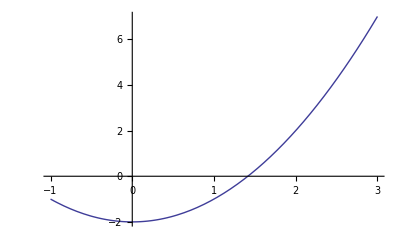

```mathematica
Plot[f1[x],{x,-1,3}]
```

```mathematica
Bisec[f_,a0_,b0_,xtol_,ytol_,pmax_]:=
Module[{c,fa,fb,fc,i},
fa=f[a0];
fb=f[b0];
c=(a0+b0)/2.00;
fc=f[c];
i=1;
While[(i≤pmax)&& (Abs[c-a0]≥xtol) && (Abs[fc]≥ytol),
If[ (Sign[fb]*Sign[fc]>0),b0=c;fb=fc;],i++]
a0=c;
fa=fc;
i=i+1;c=(a0+b0)/2.0;fc=f[c]
c]
```

```mathematica
f2[x_]:=Sin[x]
```

```mathematica
Bisec[f2,2,4,0.00000001,0.00000001,9]
```